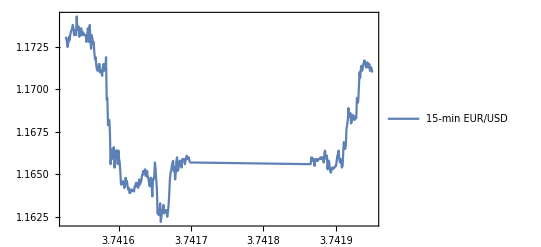

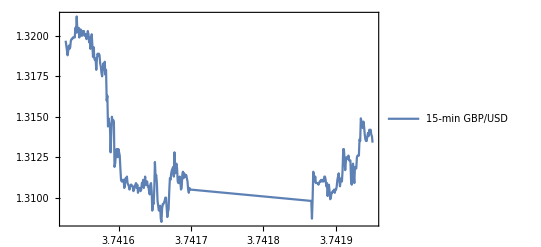

```mathematica
EURUSD=Import["/Users/wanghaibiao/Desktop/15-min.xlsx",{"Data",1,Table[i,{i,2,289}],{1,3}}];
eurusd=Import["/Users/wanghaibiao/Desktop/15-min.xlsx",{"Data",1,Table[i,{i,2,289}],3}];
GBPUSD=Import["/Users/wanghaibiao/Desktop/15-min.xlsx",{"Data",1,Table[i,{i,2,289}],{1,2}}];
gbpusd=Import["/Users/wanghaibiao/Desktop/15-min.xlsx",{"Data",1,Table[i,{i,2,289}],2}];
date=Import["/Users/wanghaibiao/Desktop/15-min.xlsx",{"Data",1,Table[i,{i,2,289}],1}];
DateListPlot[EURUSD,PlotLegends->Placed[{"15-min EUR/USD"},Above]]
DateListPlot[GBPUSD,PlotLegends->Placed[{"15-min GBP/USD"},Above]]
```

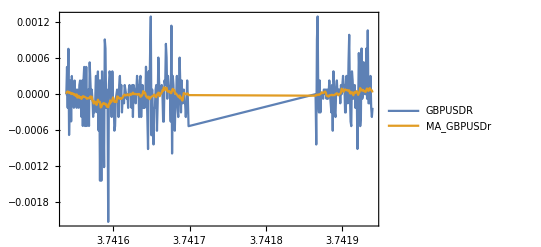

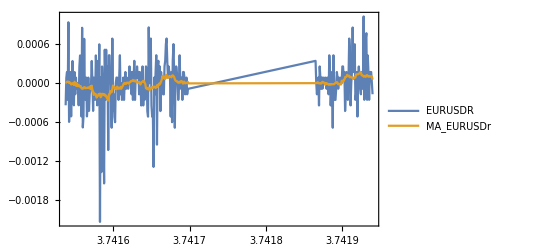

```mathematica
gbpusdr=Differences[Log[gbpusd]];
eurusdr=Differences[Log[eurusd]];
GBPUSDr=Table[{date[[i+12]],gbpusdr[[i+12]]},{i,1,264}];EURUSDr=Table[{date[[i+12]],eurusdr[[i+12]]},{i,1,264}];
mMAgbpusdr=MovingAverage[gbpusdr,24];
mMAeurusdr=MovingAverage[eurusdr,24];
mMAGBPUSDr=Table[{date[[i+12]],mMAgbpusdr[[i]]},{i,1,264}];mMAEURUSDr=Table[{date[[i+12]],mMAeurusdr[[i]]},{i,1,264}];
DateListPlot[{GBPUSDr,mMAGBPUSDr},PlotRange->{All,All},PlotLegends->Placed[{"GBPUSDR","MA_GBPUSDr"},Above]]
DateListPlot[{EURUSDr,mMAEURUSDr},PlotRange->{All,All},PlotLegends->Placed[{"EURUSDR","MA_EURUSDr"},Above]]
```

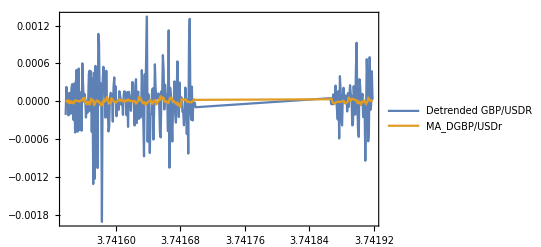

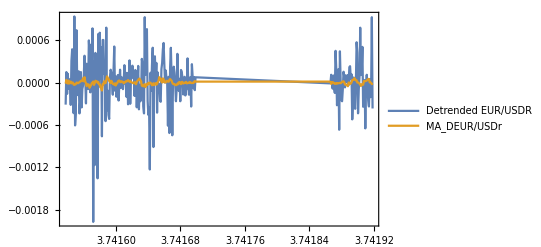

```mathematica
Dgbpusdr= Take[Drop[gbpusdr,12],264]-mMAgbpusdr;
Deurusdr= Take[Drop[eurusdr,12],264]-mMAeurusdr;
DGBPUSDr=Table[{date[[i+12]],Dgbpusdr[[i+12]]},{i,1,240}];
DEURUSDr=Table[{date[[i+12]],Deurusdr[[i+12]]},{i,1,240}];
mMADgbpusdr=MovingAverage[Dgbpusdr,24];
mMADeurusdr=MovingAverage[Deurusdr,24];
mMADGBPUSDr=Table[{date[[i+12]],mMADgbpusdr[[i]]},{i,1,240}];mMADEURUSDr=Table[{date[[i+12]],mMADeurusdr[[i]]},{i,1,240}];
DateListPlot[{DGBPUSDr,mMADGBPUSDr},PlotRange->{All,All},PlotLegends->Placed[{"Detrended GBP/USDR","MA_DGBP/USDr"},Above]]
DateListPlot[{DEURUSDr,mMADEURUSDr},PlotRange->All,PlotLegends->Placed[{"Detrended EUR/USDR","MA_DEUR/USDr"},Above]]
```

```mathematica
NSolve[m+theta==Mean[Dgbpusdr*100]&&sigma^2+theta^2==Variance[Dgbpusdr*100]&&(2*theta^3+3sigma^2*theta)/(sigma^2+theta^2)^1.5==Skewness[Dgbpusdr*100]&&sigma>0,{m,theta,sigma},Reals]
NSolve[m+theta==Mean[Deurusdr*100]&&sigma^2+theta^2==Variance[Deurusdr*100]&&(2*theta^3+3sigma^2*theta)/(sigma^2+theta^2)^1.5==Skewness[Deurusdr*100]&&sigma>0,{m,theta,sigma},Reals]
```

{{theta→-0.00349957,sigma→0.0402354,m→0.00341675}}

{{theta→-0.00918753,sigma→0.0359339,m→0.00922951}}

```mathematica
Subscript[θ, 1]=-0.003499565449860418;
Subscript[m, 1]=0.0034167472425751313;
Subscript[σ, 1]=0.04023542141696879;
Subscript[θ, 2]=-0.009187529989348006;
Subscript[m, 2]=0.009229512297831689;
Subscript[σ, 2]=0.03593391413255245;
```

```mathematica
F=Function[x,((2*Exp[Subscript[θ, 1]*(x-Subscript[m, 1])/Subscript[σ, 1]^2])/(Subscript[σ, 1]*Sqrt[2*Pi]*Gamma[1]))*((x-Subscript[m, 1])^2/(2*Subscript[σ, 1]^2+Subscript[θ, 1]^2))^0.25*BesselK[0.5,Sqrt[(x-Subscript[m, 1])^2*(2*Subscript[σ, 1]^2+Subscript[θ, 1]^2)]/Subscript[σ, 1]^2]][x]
```

17.5411 ⅇ^(-2.16171 (-0.00341675+x)-35.2149 √((-0.00341675+x)^2)) (1+0./(√((-0.00341675+x)^2)))

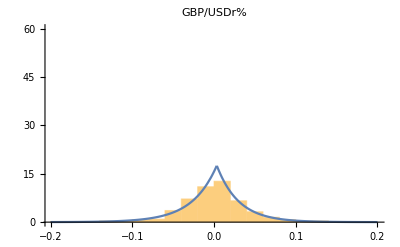

```mathematica
Show[Histogram[Dgbpusdr*100,Automatic,"ProbabilityDensity"],Plot[F,{x,-0.2,0.2},PlotRange->{Full,Full}],PlotRange->{All,{0,60}},PlotLabel->"GBP/USDr%"]
```

```mathematica
G=Function[x,((2*Exp[(Subscript[θ, 2])*(x-Subscript[m, 2])/Subscript[σ, 2]^2])/(Subscript[σ, 2]*Sqrt[2*Pi]*Gamma[1]))*((x-Subscript[m, 2])^2/(2*Subscript[σ, 2]^2+Subscript[θ, 2]^2))^0.25*BesselK[0.5,Sqrt[(x-Subscript[m, 2])^2*(2*Subscript[σ, 2]^2+Subscript[θ, 2]^2)]/Subscript[σ, 2]^2]][x]
```

19.3641 ⅇ^(-7.11524 (-0.00922951+x)-39.994 √((-0.00922951+x)^2)) (1+0./(√((-0.00922951+x)^2)))

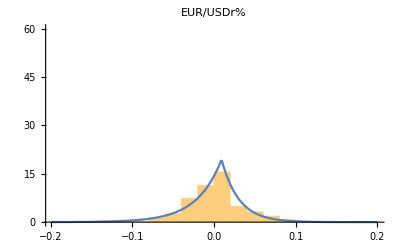

```mathematica
Show[Histogram[Deurusdr*100,Automatic,"ProbabilityDensity"],Plot[G,{x,-0.2,0.2},PlotRange->{Full,Full}],PlotRange->{All,{0,60}},PlotLabel->"EUR/USDr%"]
```

```mathematica
𝒟1=ProbabilityDistribution[F,{x,-Infinity,Infinity}];
DistributionFitTest[Dgbpusdr*100,𝒟1,"PearsonChiSquare"]
𝒟2=ProbabilityDistribution[G,{x,-Infinity,Infinity}];
DistributionFitTest[Deurusdr*100,𝒟2,"PearsonChiSquare"]
```

0.732542

0.120191

```mathematica
R12=Sin[Pi*KendallTau[Dgbpusdr*100,Deurusdr*100]/2];
R={{1,R12},{R12,1}};
MatrixForm[R]
```

(1 | 0.734649
0.734649 | 1)

```mathematica
L1=Dgbpusdr*100;
L2=Deurusdr*100;
```

```mathematica
data=Table[{L1[[i]],L2[[i]]},{i,1,264}];
```

```mathematica
EstimatedDistribution[data,CopulaDistribution[{"MultivariateT",R,v},{StudentTDistribution[v],StudentTDistribution[v]}],ParameterEstimator->"MaximumLikelihood"]
```

CopulaDistribution[{MultivariateT,{{1,0.734649},{0.734649,1}},4108.38},{StudentTDistribution[4108.38],StudentTDistribution[4108.38]}]

```mathematica
ν=4108.382441141726;
```

```mathematica
A=CholeskyDecomposition[R];
dist=ProductDistribution[NormalDistribution[],NormalDistribution[],ChiSquareDistribution[ν]];
z1=RandomVariate[MarginalDistribution[dist,1],264];
z2=RandomVariate[MarginalDistribution[dist,2],264];
s=RandomVariate[MarginalDistribution[dist,3],264];
For[i=1,i≤264,i++,
Subscript[s, i]=s[[i]];
Subscript[y, i]=A.{z1[[i]],z2[[i]]};
Subscript[x, i]=Sqrt[ν]/Sqrt[Subscript[s, i]]*Subscript[y, i]];
x1=Table[Subscript[x, i][[1]],{i,264}];
x2=Table[Subscript[x, i][[2]],{i,264}];
Subscript[u, 1]=CDF[StudentTDistribution[ν],x1];
Subscript[u, 2]=CDF[StudentTDistribution[ν],x2];
```

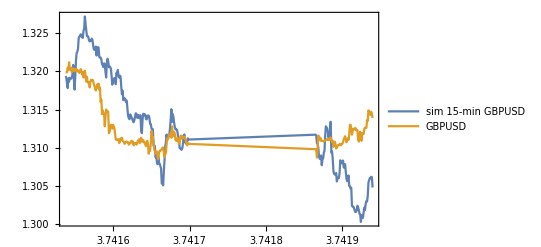

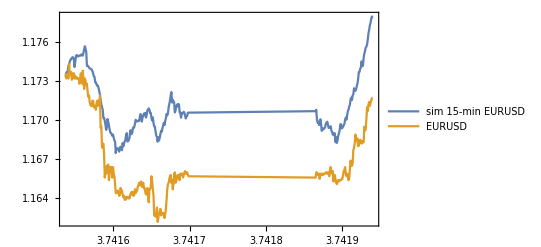

```mathematica
Subscript[Sim1, 0]=Take[Drop[gbpusd,11],1][[1]];
Subscript[Sim2, 0]=Take[Drop[eurusd,11],1][[1]];
S1=Take[Drop[gbpusd,12],264];
S2=Take[Drop[eurusd,12],264];
dates=Take[Drop[date,12],264];
Subscript[L, 1]=InverseCDF[𝒟1,Subscript[u, 1]];
Subscript[L, 2]=InverseCDF[𝒟2,Subscript[u, 2]];
For[t=1,t≤264,t++,
Subscript[L, 1,t]=Subscript[L, 1][[t]];
Subscript[L, 2,t]=Subscript[L, 2][[t]];
Subscript[Sim1, t]=Subscript[Sim1, t-1]*Exp[mMAgbpusdr[[t]]+Subscript[L, 1,t]/100];
Subscript[Sim2, t]=Subscript[Sim2, t-1]*Exp[mMAeurusdr[[t]]+Subscript[L, 2,t]/100]];
Sm1=Table[{dates[[t]],Subscript[Sim1, t]},{t,1,264}];
Sm2=Table[{dates[[t]],Subscript[Sim2, t]},{t,1,264}];
DateListPlot[{Sm1,Table[{dates[[t]],S1[[t]]},{t,1,264}]},PlotLegends->Placed[{"sim 15-min GBPUSD","GBPUSD"},Above]]
DateListPlot[{Sm2,Table[{dates[[t]],S2[[t]]},{t,1,264}]},PlotLegends->Placed[{"sim 15-min EURUSD","EURUSD"},Above]]
```